```mathematica
Clear[μ,κ,λ,LLL,RG,RGinit]
kap[μ_,κ_,λ_]:=(κ λ (1+μ)^2)/(1+κ μ)^2
lam[μ_,κ_,λ_]:=(κ+μ)^2/(1+κ μ)^2
Factor[D[kap[μ,κ,λ],μ]]
Factor[D[lam[μ,κ,λ],μ]]
```

-(2 (-1+κ) κ λ (1+μ))/(1+κ μ)^3

-(2 (-1+κ) (1+κ) (κ+μ))/(1+κ μ)^3

```mathematica
Clear[κ,λ,LLL,RG,RGinit]
RGinit={μ,1}
RG[LLL_]:=Factor[{(κ λ (1+μ)^2)/(1+κ μ)^2,(κ+μ)^2/(1+κ μ)^2}/.κ->LLL[[1]]/.λ->LLL[[2]]]
```

{μ,1}

```mathematica
L=RGinit
```

{μ,1}

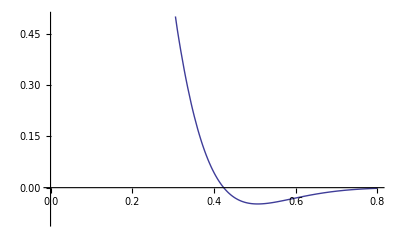

```mathematica
L=RG[L];
Plot[Log[Together[L[[2]]/2*(L[[1]]+1/L[[1]])]]/.μ->1/x,{x,.001,0.8},AxesOrigin->{0,0},PlotRange->{{0,0.8},{-0.1,0.5}}]
```

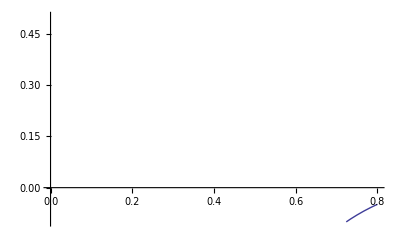

```mathematica
Plot[Log[Factor[L[[2]]/2*(L[[1]]+1/L[[1]])]]/.μ->1/x,{x,.001,0.8},AxesOrigin->{0,0},PlotRange->{{0,0.8},{-0.1,0.5}}]
```

```mathematica
Jaco = Factor[{{D[kap[μ,κ,λ],κ], D[kap[μ,κ,λ],λ]},{D[lam[μ,κ,λ],κ],D[lam[μ,κ,λ],λ]}}];
Jaco/.{κ->1,λ->1,μ->3}//MatrixForm
```

(-1/2 | 1
-1 | 0)

```mathematica
Jev1[μ_,κ_,λ_]:=-1/(2 (1+κ μ)^3)(1+μ) (-λ-λ μ+κ λ μ+κ λ μ^2+√((-λ-λ μ+κ λ μ+κ λ μ^2)^2-4 (-2 κ^2-2 κ μ-2 κ^3 μ+2 κ μ^3+2 κ^3 μ^3+2 κ^2 μ^4)));
Jev2[μ_,κ_,λ_]:=-1/(2 (1+κ μ)^3)(1+μ) (-λ-λ μ+κ λ μ+κ λ μ^2-√((-λ-λ μ+κ λ μ+κ λ μ^2)^2-4 (-2 κ^2-2 κ μ-2 κ^3 μ+2 κ μ^3+2 κ^3 μ^3+2 κ^2 μ^4)));
```

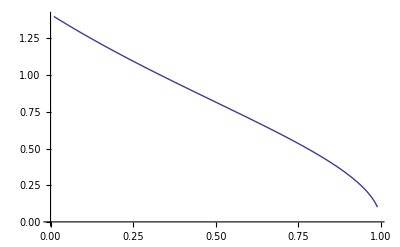

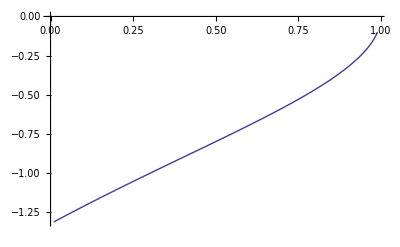

```mathematica
Plot[Abs[Jev1[μ,κ,λ]/.{κ->1,λ->1,μ->1/x}],{x,0.01,0.99},AxesOrigin->{0,0}]
Plot[Im[Jev1[μ,κ,λ]/.{κ->1,λ->1,μ->1/x}],{x,0.01,0.99},AxesOrigin->{0,0}]
```

```mathematica
Clear[μ,κ,ϕ,λ,LLL,RG,RGinit]
kap[r_,ϕ_]:=(κ λ (1+μ)^2)/(1+κ μ)^2/.{κ->(r*Cos[ϕ]+1),λ->(r*Sin[ϕ]+1)}
lam[r_,ϕ_]:=(κ+μ)^2/(1+κ μ)^2/.{κ->(r*Cos[ϕ]+1),λ->(r*Sin[ϕ]+1)}
1+r*Cos[ϕ]==Factor[kap[r,ϕ]]
1+r*Sin[ϕ]==Factor[lam[r,ϕ]]
Clear[μ,ϕ]
```

1+r Cos[ϕ]==((1+μ)^2 (1+r Cos[ϕ]) (1+r Sin[ϕ]))/(1+μ+r μ Cos[ϕ])^2

1+r Sin[ϕ]==(1+μ+r Cos[ϕ])^2/(1+μ+r μ Cos[ϕ])^2

```mathematica
FullSimplify[Expand[(1+r Cos[ϕ]) (1+μ+r μ Cos[ϕ])^2-(1+μ)^2 (1+r Cos[ϕ]) (1+r Sin[ϕ])==0]]
FullSimplify[Expand[(1+r Sin[ϕ])(1+μ+r μ Cos[ϕ])^2-(1+μ+r Cos[ϕ])^2==0]]
μ=3.01;
ϕ=0.4;
Solve[FullSimplify[Expand[(1+r Cos[ϕ]) (1+μ+r μ Cos[ϕ])^2-(1+μ)^2 (1+r Cos[ϕ]) (1+r Sin[ϕ])==0]],r]
Solve[FullSimplify[Expand[(1+r Sin[ϕ])(1+μ+r μ Cos[ϕ])^2-(1+μ+r Cos[ϕ])^2==0]],r]
Clear[μ,ϕ];
```

r (1+r Cos[ϕ]) (μ Cos[ϕ] (2+2 μ+r μ Cos[ϕ])-(1+μ)^2 Sin[ϕ])==0

r (-1+μ^2) Cos[ϕ] (2+r Cos[ϕ])+r (1+μ+r μ Cos[ϕ])^2 Sin[ϕ]==0

{{r→-2.07811},{r→-1.0857},{r→0}}

{{r→-2.58865-0.592908 ⅈ},{r→-2.58865+0.592908 ⅈ},{r→0}}

```mathematica
kap[μ_,κ_,λ_]:=(κ λ (1+μ)^2)/(1+κ μ)^2
lam[μ_,κ_,λ_]:=(κ+μ)^2/(1+κ μ)^2
```

```mathematica
kap[μ,κ,λ]/.λ->lam[μ,κ,λ]
```

(κ (1+μ)^2 (κ+μ)^2)/(1+κ μ)^4

```mathematica
Clear[κ,λ,LLL,RG,RGinit]
RGinit={μ,1}
RG[LLL_]:=Factor[{(κ λ (1+μ)^2)/(1+κ μ)^2,(κ+μ)^2/(1+κ μ)^2}/.κ->LLL[[1]]/.λ->LLL[[2]]]
RGinit2={μ}
RG2[LLL_]:=Factor[{(κ (1+μ)^2 (κ+μ)^2)/(1+κ μ)^4}/.κ->LLL[[1]]]
```

{μ,1}

{μ}

```mathematica
L=RGinit
L2=RGinit2
```

{μ,1}

{μ}

```mathematica
L=RG[L]
L2=RG2[L2]
```

{(μ (1+μ)^2)/((1+μ^2)^2),(4 μ^2)/((1+μ^2)^2)}

{(4 μ^3 (1+μ)^2)/((1+μ^2)^4)}

```mathematica
RG[L]
```

{(4 μ^3 (1+μ)^4)/((1+3 μ^2+2 μ^3+2 μ^4)^2),(μ^2 (2+2 μ+3 μ^2+μ^4)^2)/((1+3 μ^2+2 μ^3+2 μ^4)^2)}

```mathematica
λ
```

λ